```mathematica
Get["D:\\Dhruv\\MITACS_Summer_22\\Codes\\cartPendulum.m"]
```

## Main Functions

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
polePlacementFeedback1[p_,xm_,xdotm_,θm_,θdotm_,xff_,xdotff_,θff_,θdotff_,uff_,A_] := Module[{fx,nDim,xState ,x,xdot,θ,θdot,x2dot,θ2dot,u,L,Af,Bf,Cf,ssm,K,uStar,uFinal,i,j},
nDim = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Bf = Table[Table[Bf[[i]],{i,j,j}],{j,1,nDim}];
Cf = {1,1,1,1};
x = xm - xff;xdot =  xdotm - xdotff;θ =  θm - θff;θdot =  θdotm - θdotff;u = uff; 

ssm = StateSpaceModel[{Table[Table[Af[[i]][[j]],{j,1,nDim}],{i,1,nDim}],Table[Bf[[i]],{i,1,nDim}],Table[Table[Cf[[i]],{i,j,nDim}],{j,1,1}]},SamplingPeriod->None,SystemsModelLabels->None];
K = StateFeedbackGains[ssm,p];
uStar = -K.xState;
uFinal = u + uStar]

polePlacementFeedback2[p_,xm_,xdotm_,θm_,θdotm_,xff_,xdotff_,θff_,θdotff_,uff_,A_] := Module[{fx,nDim,xState ,x,xdot,θ,θdot,x2dot,θ2dot,u,L,Af,Bf,K,uStar,uFinal,i,j,M,charPoly,preMultiplier},
nDim = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
x = xm - xff;xdot =  xdotm - xdotff;θ =  θm - θff;θdot =  θdotm - θdotff;u = uff; 

M = Table[If[i!= 0,MatrixPower[Af,i].Bf,IdentityMatrix[nDim].Bf],{i,0,nDim-1}]ᵀ;
charPoly = IdentityMatrix[nDim];
For[i = 1,i <= nDim,i++,
charPoly = charPoly.(Af - p[[i]]*IdentityMatrix[nDim]);
];
preMultiplier = Table[If[i != nDim,0,1],{i,1,nDim}];
K = preMultiplier.(Inverse[M].charPoly) ;
uStar = -K.xState;
uFinal = u + uStar]

TestSwingUpPolePlacementFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,p},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
p={-0.1,-0.2,-4,-3};
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

u[t_]:=Piecewise[{{polePlacementFeedback2[p,x[t],xdot[t],θ[t],θdot[t],xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A],0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};
   
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=Piecewise[{{polePlacementFeedback2[p,xs[t],xdots[t],θs[t],θdots[t],xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A],0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolveValue::ndsz: At t$303484 == 4.90628, step size is effectively zero; singularity or stiff system suspected.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$303484 near {t$303484} = {4.99123666875714401720831592257354714092798531055450439453125}. NIntegrate obtained 2.21158×10^147 and 2.08033×10^147 for the integral and error estimates.

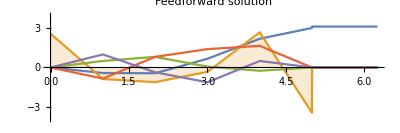

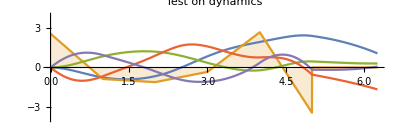

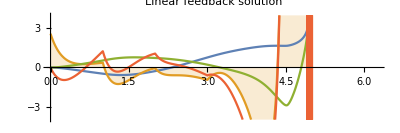

```mathematica
n = 5; τ = 5; τ1 = τ*1.25 ; A = 0.2; 
ICs = {0,0,0,0};
p={-0.1,-0.2,-0.4,-0.3};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A];{x1c,xdot1c,θ1c,θdot1c,u1c,J}=TestSwingUpPolePlacementFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],u1c[t]-u1a[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","ufb"},PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

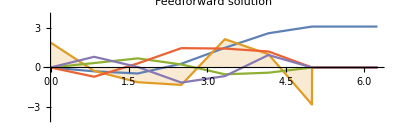

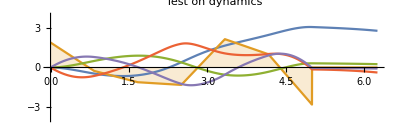

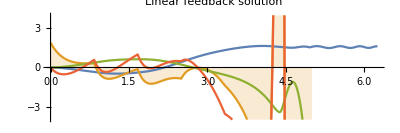

```mathematica
n = 6; τ = 5; τ1 = τ*1.25 ; A = 0.2; 
ICs = {0,0,0,0};
p={-0.1,-0.2,-0.4,-0.3};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A];{x1c,xdot1c,θ1c,θdot1c,u1c,J}=TestSwingUpPolePlacementFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],u1c[t]-u1a[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","ufb"},PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$176057 near {t$176057} = {4.89950189943794}. NIntegrate obtained 7.03436 and 0.000295644 for the integral and error estimates.

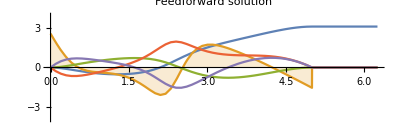

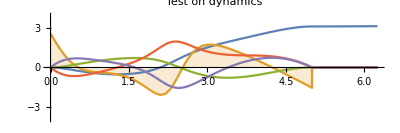

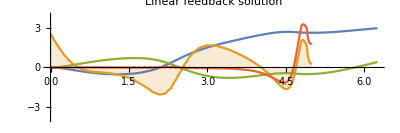

```mathematica
n = 50; τ = 5; τ1 = τ*1.25 ; A = 0.2; 
ICs = {0,0,0,0};
p={-0.1,-0.2,-0.4,-0.3};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A];{x1c,xdot1c,θ1c,θdot1c,u1c,J}=TestSwingUpPolePlacementFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],u1c[t]-u1a[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","ufb"},PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

## Understand the Reference Model

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-Graphics-

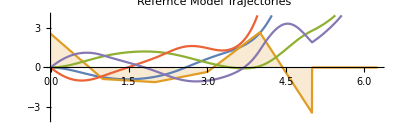

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
linearizeSystem[xs_,xdots_,θs_,θdots_,us_,A_] := Module[{Af,Bf,nDim,xState,x,xdot,θ,θdot,x2dot,θ2dot,fx,L,u},
nDim = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
x = xs;xdot = xdots;θ =  θs;θdot =  θdots;u = us;
{Af,Bf}]


testRefModel[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,Af,Bf},

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
Af[t_] := linearizeSystem[xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A][[1]];
Bf[t_] := linearizeSystem[xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A][[2]];
eq={x'[t]       ==(Af[t].{x[t],xdot[t],θ[t],θdot[t]} + Bf[t]*uff[t])[[1]],
       xdot'[t]==(Af[t].{x[t],xdot[t],θ[t],θdot[t]} + Bf[t]*uff[t])[[2]],
       θ'[t]       ==(Af[t].{x[t],xdot[t],θ[t],θdot[t]} + Bf[t]*uff[t])[[3]],
       θdot'[t]==(Af[t].{x[t],xdot[t],θ[t],θdot[t]} + Bf[t]*uff[t])[[4]]};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff,J}]
n = 5; τ = 5; τ1 = τ*1.25 ; A = 0.2; 
ICs = {0,0,0,0};
p={-0.1,-0.2,-0.4,-0.3};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testRefModel[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"Refernce Model Trajectories",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

## Choosing Pole Locations

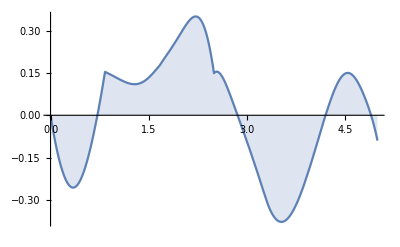
-Graphics-u(t)

-Graphics-

-Graphics-

```mathematica
n = 6; τ = 5; τ1 = τ*1.25 ; A = 0.2; 
ICs = {0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A];
p={-0.1,-0.2,-0.4,-0.3};
uFeedback[time_] := polePlacementFeedback2[p,x1b[time],xdot1b[time],θ1b[time],θdot1b[time],x1a[time],xdot1a[time],θ1a[time],θdot1a[time],u1a[time],A] - u1a[time];
Labeled[Plot[uFeedback[t],{t,0,τ},Filling->{1->Axis}],"u(t)"]
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

## Debugging Scripts

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
polePlacementFeedback2[p_,xm_,xdotm_,θm_,θdotm_,xff_,xdotff_,θff_,θdotff_,uff_,A_] := Module[{fx,nDim,xState ,x,xdot,θ,θdot,x2dot,θ2dot,u,L,Af,Bf,K,uStar,uFinal,i,j,M,charPoly,preMultiplier},
nDim = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
x = xm - xff;xdot =  xdotm - xdotff;θ =  θm - θff;θdot =  θdotm - θdotff;u = uff; 

M = Table[If[i!= 0,MatrixPower[Af,i].Bf,IdentityMatrix[nDim].Bf],{i,0,nDim-1}]ᵀ;
charPoly = IdentityMatrix[nDim];
For[i = 1,i <= nDim,i++,
charPoly = charPoly.(Af - p[[i]]*IdentityMatrix[nDim]);
];
preMultiplier = Table[If[i != nDim,0,1],{i,1,nDim}];
K = preMultiplier.(Inverse[M].charPoly) ;
uStar = -K.xState;
uFinal = u + uStar]

κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
p={-0.1,-0.2,-4,-3};
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

u[t_]:=polePlacementFeedback2[p,x[t],xdot[t],θ[t],θdot[t],xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
```

Remove::rmnsm: There are no symbols matching "Global`*".

NDSolveValue::ndsz: At t == 4.74436, step size is effectively zero; singularity or stiff system suspected.

```mathematica
us[t_]:=polePlacementFeedback[p,xs[t],xdots[t],θs[t],θdots[t],xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A];

J = NIntegrate[us[t]^2,{t,0,τ}];

{xs,xdots,θs,θdots,us,J}
```

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
Af = {{1,2},{3,4}};n = 2;
Bf = {1,2};
Bf = Table[Table[Bf[[i]],{i,j,j}],{j,1,n}];
Cf = {1,2};
p = {-0.1,-2.5};
ssm = StateSpaceModel[{Table[Table[Af[[i]][[j]],{j,1,n}],{i,1,n}],Table[Bf[[i]],{i,1,n}],Table[Table[Cf[[i]],{i,j,n}],{j,1,1}]},SamplingPeriod->None,SystemsModelLabels->None];
K = StateFeedbackGains[ssm,p]
```

Remove::rmnsm: There are no symbols matching "Global`*".

{{3.1,2.25}}

```mathematica
(* Pole Placement using Ackermann's Formula*)
Clear["Global`*"]; 
Remove["Global`*"];
Af = {{1,2,3,4},{3,4,5,6},{3,4,1,6},{3,4,2,6}};n = 4;
Bf = {1,2,3,4};
p = {-0.1,-2.5,-2,-3};
M = Table[If[i!= 0,MatrixPower[Af,i].Bf,IdentityMatrix[n].Bf],{i,0,n-1}]ᵀ;
charPoly = IdentityMatrix[n];
For[i = 1,i <= n,i++,
charPoly = charPoly.(Af - p[[i]]*IdentityMatrix[n]);
]
preMultiplier = Table[If[i != n,0,1],{i,1,n}];
K = preMultiplier.(Inverse[M].charPoly)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

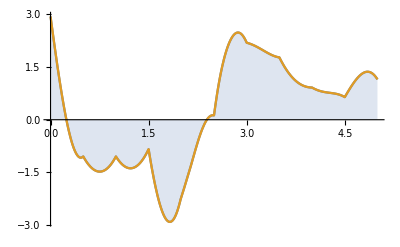
-Graphics-u(t)

```mathematica
n = 10; τ = 5; τ1 = τ*1.25 ; A = 0.2; 
ICs = {0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A];
p={-0.1,-0.2,-4,-3};
uFeedback1[time_] := polePlacementFeedback1[p,x1b[time],xdot1b[time],θ1b[time],θdot1b[time],x1a[time],xdot1a[time],θ1a[time],θdot1a[time],u1a[time],A];
uFeedback2[time_] := polePlacementFeedback2[p,x1b[time],xdot1b[time],θ1b[time],θdot1b[time],x1a[time],xdot1a[time],θ1a[time],θdot1a[time],u1a[time],A];
Labeled[Plot[{uFeedback1[t],uFeedback2[t]},{t,0,τ},Filling->{1->Axis}],"u(t)"]
```